1.S pomočjo Mathematice izračunaj:

```mathematica
(1/3+ 1/6)^2
```

1/4

```mathematica
3/(6/8)
```

4

```mathematica
Sin[Pi/2]
```

1

```mathematica
E^Log[7]
```

7

```mathematica
?Log
```

## 2. Poenostavi naslednje izraze :

```mathematica
FullSimplify[((3+4x)/(2+5x))^2 + ((2+x)/(1-x))^2]
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

```mathematica
Simplify[x/y + y/x +2]
```

(x+y)^2/(x y)

```mathematica
izraz =(x^2 + y^2)^2 - 2*(x*y)^2
```

-2 x^2 y^2+(x^2+y^2)^2

```mathematica
izraz
```

-2 x^2 y^2+(x^2+y^2)^2

```mathematica
Simplify[izraz]
```

x^4+y^4

```mathematica
Simplify[(Sin[x])^2 + (Cos[x])^2]
```

1

```mathematica
Simplify[2*Sin[x]*Cos[x]]
```

Sin[2 x]

```mathematica
izraz1=(Tan[Pi/8])^4 + (Cot[Pi/8])^4
```

Cot[π/8]^4+Tan[π/8]^4

```mathematica
FullSimplify@izraz1
```

34

```mathematica
ClearAll[izraz1]
```

```mathematica
FullSimplify[Sqrt[278 + 42Sqrt[5] - 12Sqrt[6] - 28Sqrt[30]]]
```

3+7 √5-2 √6

## 3. Razstavi izraz (x + xy + (y))^10. Razstavi še izraze sin(x + y). (Nasvet: TrigExpand)

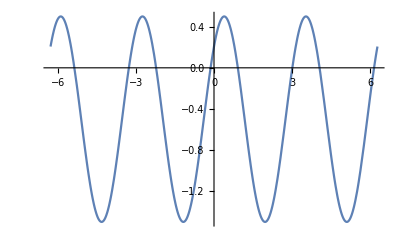

```mathematica
Plot[Sin[2x + Pi/4] - 1/2, {x, -2 Pi, 2Pi}]
```

```mathematica
Plot[Sin[2x + Pi/4] - 1/2, {x, -2Pi, 2Pi}]
```

-Graphics-

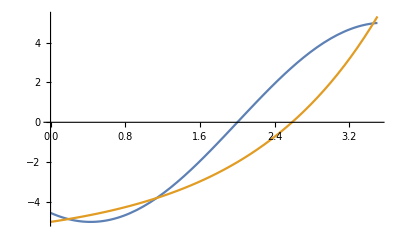

```mathematica
f[x_] := 5*Sin[x-2]
g[x_] := 2^x - 6

Plot[{f[x], g[x]}, {x, 0, 3.5}]
```

```mathematica
NALOGA 8
```

```mathematica
a=3^200 + 20
b=2^300 + 30
```

265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044021

2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397406

```mathematica
a== b
```

False

```mathematica
3 == 3 - 1 +1
```

True

```mathematica
a < b
```

False

```mathematica
a > b
```

True

### NALOGA 9

```mathematica
Solve[x^2 + 4x +2 ==0, x]
```

{{x→-2-√2},{x→-2+√2}}

```mathematica
Solve[x^2 + 4x + 5 == 0, x]
```

{{x→-2-ⅈ},{x→-2+ⅈ}}

### NALOGA 10

```mathematica
Reduce[x^4 == 1, x]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

### NALOGA 11

```mathematica
ClearAll[x]
f[x_] := (x^2 - (x^2)^(1/3)) * E^x
```

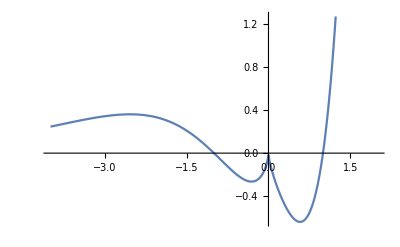

```mathematica
Plot[f[x], {x, -4, 2}]
```

```mathematica
Solve[f[x]== 0, x]
```

{{x→0},{x→1}}